Зад. 1 Да се пресметне производната на функцията

f(x) = x^3- cos x √(2x-8),

като се използва дефиницията за производна. Резултатът да се провери с помощта на вградената функция за диференциране.

```mathematica
f[x_]:=x^3-Cos[x]Sqrt[2x-8]
Limit[(f[x+h]-f[x])/h,h->0]//Factor
D[f[x],x]//Factor
```

(6 √(-4+x) x^2-√2 Cos[x]-8 √2 Sin[x]+2 √2 x Sin[x])/(2 √(-4+x))

(6 √(-4+x) x^2-√2 Cos[x]-8 √2 Sin[x]+2 √2 x Sin[x])/(2 √(-4+x))

Зад.2 Да се анимира приближението на функцията sin(x) + cos(x) в интервала [0,10], с полиноми на Тейлър от степени от 1 до 30 последователно, около т. x_0=0.
На всяка стъпка от анимацията да се визуализират едновременно графиката на функцията и графика на съответното приближение.

```mathematica
f[x_]:=Sin[x]+Cos[x];
x0=0;
Manipulate[Plot[{f[x],f[x0]+Sum[ReplaceAll[D[f[xx],{xx,k}],xx->x0 ](x-x0)^k/(k!),{k,1,order}]},{x,0,10},PlotRange->{{0,10},{-3,3}}],
{order,1,30,1}
]
```

Зад. 3 Да се намери точката от графиката на функцията g(x) =(sin (4x))/(e^(x^3)), намираща се на най-малко разстояние от точката с координати (-0.5,  0.5).

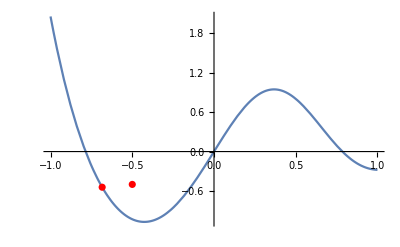

```mathematica
g[x_]:=Sin[4x]/Exp[x^3];
distance[x_]:=Sqrt[(x+0.5)^2+(g[x]+0.5)^2]
mindData=Minimize[distance[x],x];
Show[Plot[Sin[4x]/Exp[x^3],{x,-1,1}],
ListPlot[{{x,g[x]}/.mindData[[2]],{-0.5,-0.5}},PlotStyle->Red]
]
```

Зад.4 Телескопът Хъбъл е изстрелян на 24.04.1990 от космическата совалка Discovery. Скоростта на Discovery по време на тази мисия от момента на изстрелване t=0, до момента на отделяне на ракетните двигатели t=126, може да се моделира с помощта на функцията

v(t) = 0.001302 t^3- 0.09029 t^2+23.61t - 3.083. 
 
Като изпозлвате този модел, оценете стойностите на минималното и максималното ускорение на совалката между моментите на излитане и отделяне на ракетните двигатели.

```mathematica
v[t_]:= 0.001302 t^3- 0.09029 t^2+23.61t-3.083;
Maximize[v'[t],0≤t≤126,t]
Minimize[v'[t],0≤t≤126,t]
```

{62.8686,{t→126.}}

{21.5229,{t→23.1157}}

Зад.5 Да се намери лицето на фигурата, заградена от графиките на функциите y=ln(x) и y=ln^2(x).

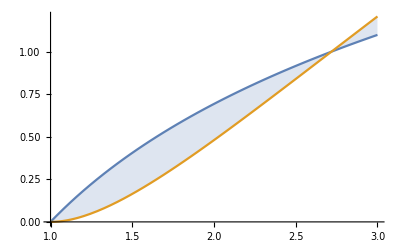

{{x→1},{x→ⅇ}}

3-ⅇ

```mathematica
Plot[{Log[x],Log[x]^2},{x,1,3},Filling->{1->{2}}]
Solve[Log[x]==Log[x]^2,x]
area=Integrate[Log[x]-Log[x]^2,{x,1,E}]
```

Зад.2 Известно е, че червените кръвни телца (еритроцити) на бозайниците, в спокойно състояние имат формата на двойно-сплеснат диск. Благодарение на тази форма, площта на повърхнината на еритроцитите е много голяма в сравнение с обема им.
Това спомага кислородът и въглеродният диоксид да дифундират по-лесно през мембранта на клетките, като същеврменно размерите и гъвкавостта им, им позволяват да преминават дори през най-малките кръвоносни съдове. Един възможен начин да се опише геометричната форма на еритроцитите е следният:

z = ± D_0 √(1 - (4(x^2+y^2))/D_0^2) (a_0+(a_1(x^2+y^2))/D_0^2 + ((a_2(x^2+y^2))^2)/D_0^4),

където D_0= 7.82 μm е диаметърът на клетката, а a_0=0.0518, a_1=2.0026, и  a_2= -4.491 са експериментално установени параметри. Да се изобрази графично формата на клетката и да се пресметнe обема и.

```mathematica
D0=7.82; a0=0.0518; a1=2.0026; a2=-4.491;
RBCshape[x_,y_]:=D0 √(1-(4(x^2+y^2))/D0^2)(a0+(a1(x^2+y^2))/D0^2+(a2(x^2+y^2)^2)/D0^4)
Plot3D[{-RBCshape[x,y],RBCshape[x,y]},{x,-4,4},{y,-4,4},PlotStyle->Red,Mesh->None]
```

-Graphics3D-

```mathematica
(*Първи начин: Намираме проекцията на двете повърхнини в равнината x-y и определяме границите на интегриране*)
Quiet[Reduce[D0 √(1-(4(x^2+y^2))/D0^2)(a0+(a1(x^2+y^2))/D0^2+(a2(x^2+y^2)^2)/D0^4)==0,{x,y},Reals]]
```

-3.91≤x≤3.91&&(y==-0.01 √(152881.-10000. x^2)||y==0.01 √(152881.-10000. x^2))

```mathematica
volume=2*NIntegrate[RBCshape[x,y],{x,-3.91,3.91},{y,-0.01 √(152881.-10000. x^2),0.01 √(152881.-10000. x^2)}]
```

94.0984

```mathematica
(*Втори начин: С помощта на получения резултат, дефинираме геометричната област, представялваща проекцията, и я използваме директно във функцията Integrate*)
reg=ImplicitRegion[-3.91≤ x≤3.91 && -0.01 √(152881-10000 x^2)≤y<=0.01 √(152881-10000 x^2),{x,y}];
```

```mathematica
RegionPlot[reg,PlotRange->{{-4,4},{-4,4}}]
```

-Graphics-

```mathematica
volume=2*NIntegrate[RBCshape[x,y], {x,y}∈reg]
```

94.0984

```mathematica
(*Трети и четвърти начин: троен интеграл*)
NIntegrate[1,{x,-3.91,3.91},{y,-0.01 √(152881.-10000. x^2),0.01 √(152881.-10000. x^2)},{z,-D0 √(1-(4(x^2+y^2))/D0^2)(a0+(a1(x^2+y^2))/D0^2+(a2(x^2+y^2)^2)/D0^4),D0 √(1-(4(x^2+y^2))/D0^2)(a0+(a1(x^2+y^2))/D0^2+(a2(x^2+y^2)^2)/D0^4)}]
```

94.0984

```mathematica
reg3D=ImplicitRegion[-3.91≤ x≤3.91 && 
-0.01 √(152881.-10000. x^2)≤y<=0.01 √(152881.-10000. x^2)&& 
-D0 √(1-(4(x^2+y^2))/D0^2)(a0+(a1(x^2+y^2))/D0^2+(a2(x^2+y^2)^2)/D0^4)≤z≤D0 √(1-(4(x^2+y^2))/D0^2)(a0+(a1(x^2+y^2))/D0^2+(a2(x^2+y^2)^2)/D0^4) ,{x,y,z}];
RegionPlot3D[reg3D,PlotRange->{{-4,4},{-4,4},{-2,2}},PlotStyle->Red]
```

-Graphics3D-

```mathematica
NIntegrate[1,{x,y,z}∈reg3D]
```

94.0984

```mathematica
(*Пети начин: функцията Volume*)
Volume[reg3D]
```

94.0984

```mathematica
(*Можем да пресметнем и лицето на повърхнината на клетката*)
2*NIntegrate[Sqrt[D[RBCshape[x,y],x]^2+D[RBCshape[x,y],y]^2+1],{x,-3.91,3.91},{y,-0.01 √(152881.-10000. x^2),0.01 √(152881.-10000. x^2)}]
```

134.093